# ABS Model with Theta Wake (Solution to Dynamical System)

## Solve for time-dependent Fourier Coefficients

```mathematica
ClearAll["Global`*"]
$MachineEpsilon
$MachinePrecision
```

2.22045×10^-16

15.9546

```mathematica
$Assumptions=q∈Reals
size = 500;
```

q∈ℝ

```mathematica
(*Calculate solution to theta wake*)
unm[n_Integer,m_Integer]:=Which[
(*both zero*)
m==0&&n==0,1./2.,
(*main diagonal m=n (covers n≠0)integral is 0*)
m==n,0,
(*anti-diagonal m=-n with n≠0 also 0*)
m==-n&&n=!=0,0,
(*m=0,n≠0:special closed form*)
m==0,-(1.-(-1.)^n)/((Pi n)^2.),
(*generic case:m≠0 and m≠±n*)
True,(1./(2. Pi^2. m))*((1.-(-1.)^(m+n))/(m+n)+(1.-(-1.)^(m-n))/(m-n))];
```

```mathematica
(* Define space charge and wake parameters to use *)
q=20.0;
w=1.0;
```

```mathematica
(* Build u matrix*)
umatrix = Table[unm[i,j],{i,-size,size,1},{j,-size,size,1}];//AbsoluteTiming
```

{3.82776,Null}

```mathematica
(* Build d matrix *)
dmatrix = ParallelTable[(n-q/2.)*KroneckerDelta[n,m]+(q/2.)*KroneckerDelta[-n,m],{n,-size,size,1},{m,-size,size,1},Method->"CoarsestGrained"];//AbsoluteTiming
```

{2.32405,Null}

```mathematica
(* Build total matrix *)
mmatrix = -I*(dmatrix-w*umatrix);
```

```mathematica
(* Calculate eigenvectors and eigenvalues*)
{eigenvals,eigenvects}=Eigensystem[N[mmatrix]];//AbsoluteTiming
paired = Transpose[{eigenvals,eigenvects}];
(* Sort them by mode *)
sorted = SortBy[paired,-Im[First[#]] &];
{sortedVals,sortedVecs}=Transpose[sorted];
```

{0.806348,Null}

```mathematica
(* Get solutions and multiply by arbitrary constant tbd from initial conditions*)
(*sols = Exp[sortedVals*θ]*sortedVecs;
constants = Array[α,Length[sols]];
antheta = Total[sols*constants,{1}];*)
```

```mathematica
(* Get solutions and multiply by arbitrary constant tbd from initial conditions*)
(*Matrix whose columns are eigenvectors in n-basis*)
sols = Exp[sortedVals*θ]*sortedVecs;
Vmat=Transpose[sortedVecs];              (*N x N,N=2*size+1*)
(*target Fourier coefficients for x(ψ)=1:only n=0 is 1*)
target=UnitVector[Length[Vmat],size+1];  (*index size+1 corresponds to n=0*)
(*Solve for alpha numerically (FAST)*)
alphaVec=LinearSolve[N@Vmat,N@target];
(*Now use alphaVec instead of NSolve rules*)
antheta=Total[sols*alphaVec,{1}];
```

```mathematica
(* Get total solution including azimuthal solutions*)
nvec = Range[-size,size];
azimuthalsols = Exp[1.*I*nvec*ψ];
totalsol = Total[(antheta*azimuthalsols)];
(*Get expression at θ=0 to solve for constants *)
totalsolzero = Total[(antheta*azimuthalsols)/.{θ->0}];
```

```mathematica
(* Solve for constants with constant initial condition *)
initialcondition = 1.0;
ψVals=Subdivide[-Pi,Pi,2*size+1][[;;-2]];
equations=(ψVal↦(totalsolzero/. ψ->ψVal)==initialcondition)/@ψVals;//AbsoluteTiming
(*equations =Table[(totalsolzero/.{ψ->ψi})==initialcondition,{ψi,-Pi,Pi,2.*Pi/(2.*size+1)}];//AbsoluteTiming*)
initialsols = NSolve[equations,constants];//AbsoluteTiming
```

{1.16673,Null}

{0.002962,Null}

```mathematica
(* Build solutions *)
solution[θstar_,ψstar_]:= (totalsol/.initialsols)/.{θ->θstar,ψ->ψstar};
centroid[θstar_,ψstar_]:=(1/2)*(solution[θstar,ψstar]+solution[θstar,-ψstar]);
head[θstar_]:=Abs[centroid[θstar,0.0]];
tail[θstar_]:=Abs[centroid[θstar,Pi]];
headtailamplification [θstar_]:= Abs[centroid[θstar,Pi]]/Abs[centroid[θstar,0.0]];
```

```mathematica
(*1) Freeze constants ONCE*)
tot0=Evaluate[totalsol/. initialsols];
(*2) Build a numeric function for x(θ,ψ)*)
xFun=Function[{θ,ψ},Evaluate[tot0]];
(*3) Head/tail helpers also numeric*)
centroidFun=Function[{θ,ψ},0.5 (xFun[θ,ψ]+xFun[θ,-ψ])];
xplus = Function[{θ,s},xFun[θ,-Pi*s]];
xminus = Function[{θ,s},xFun[θ,Pi*s]];
```

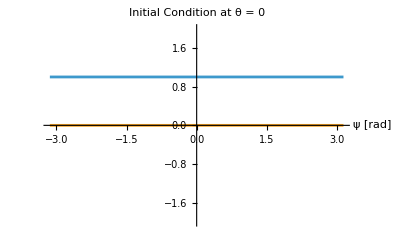

```mathematica
(*Plot using the numeric function directly*)
Plot[{Abs[xFun[0.,ψ]],Arg[xFun[0.,ψ]]},{ψ,-Pi,Pi},PlotRange->{{-Pi,Pi},{-2,2}},PlotPoints->10,
AxesLabel->{Style["ψ [rad]", Black, Large]},
LabelStyle->Directive[Larger,Black],
PlotLabel->Style["Initial Condition at θ = 0", Black, Larger], PlotLegends->{"",""},
PlotRange->{{-Pi,Pi},{-2,2}}PerformanceGoal->"Speed",Exclusions->None]
```

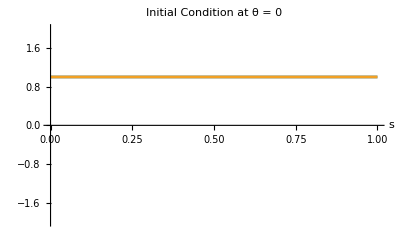

```mathematica
Plot[{Abs[xplus[0.,s]],Abs[xminus[0.,s]]},{s,0,1},PlotRange->{{0,1},{-2,2}},PlotPoints->10,
AxesLabel->{Style["s", Black, Large]},
LabelStyle->Directive[Larger,Black],
PlotLabel->Style["Initial Condition at θ = 0", Black, Larger], PlotLegends->{"",""},
PlotRange->{{-Pi,Pi},{-2,2}}PerformanceGoal->"Speed",Exclusions->None]
```

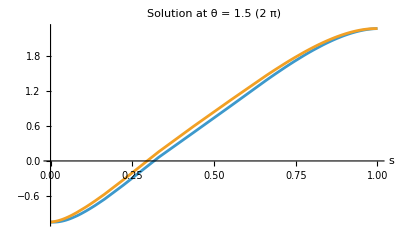

```mathematica
Plot[{Log[Abs[xplus[1.5*2*Pi,s]]],Log[Abs[xminus[1.5*2*Pi,s]]]},{s,0,1},PlotRange->{{0,1},Automatic},PlotPoints->10,
AxesLabel->{Style["s", Black, Large]},
LabelStyle->Directive[Larger,Black],
PlotLabel->Style["Solution at θ = 1.5 (2 π)", Black, Larger], PlotLegends->{"",""},
PlotRange->{{-Pi,Pi},{-2,2}}PerformanceGoal->"Speed",Exclusions->None]
```

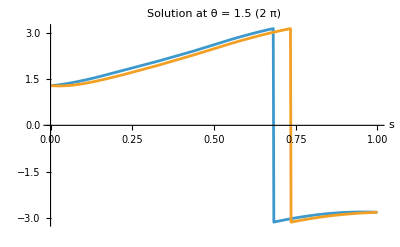

```mathematica
Plot[{Arg[xplus[1.5*2*Pi,s]],Arg[xminus[1.5*2*Pi,s]]},{s,0,1},PlotRange->{{0,1},Automatic},PlotPoints->10,
AxesLabel->{Style["s", Black, Large]},
LabelStyle->Directive[Larger,Black],
PlotLabel->Style["Solution at θ = 1.5 (2 π)", Black, Larger], PlotLegends->{"",""},
PlotRange->{{-Pi,Pi},{-2,2}}PerformanceGoal->"Speed",Exclusions->None]
```

```mathematica
(* Build ABS eigenfunctions *)
xl = Dot[sols,azimuthalsols];
cosBasis=Cos[nvec*ψ];
xlcentroid=sols.cosBasis;
ns = 20;
xlcentroidstrobe = ParallelTable[Re[(xlcentroid[[i]]/.θ->0)*Exp[-2*I*Pi*j/ns]],{i,Length[xlcentroid]},{j,0,ns}];
```

```mathematica
(* Calculate amplification factors *)
xlPi=xl/. {ψ->Pi,θ->0};
xl0=xl/. {ψ->0,θ->0};
ks = Abs[xlPi/xl0];
(*kmax = Max[ks];*)
kmax=Max[ks];
kIndex = First@Ordering[ks,-1]-size-1;
logmax = Log[kmax];
```

```mathematica
(* Plot initial condition *)
Plot[{Abs[solution[0,ψ]],Arg[solution[0,ψ]]},{ψ,-Pi,Pi},
AxesLabel->{Style["ψ [rad]", Black, Large]},
LabelStyle->Directive[Larger,Black],
PlotLabel->Style["Initial Condition at θ = 0", Black, Larger], PlotLegends->{"",""},
PlotRange->{{-Pi,Pi},{-2,2}}, PlotPoints->10, PerformanceGoal->"Speed"]
```

-Graphics-

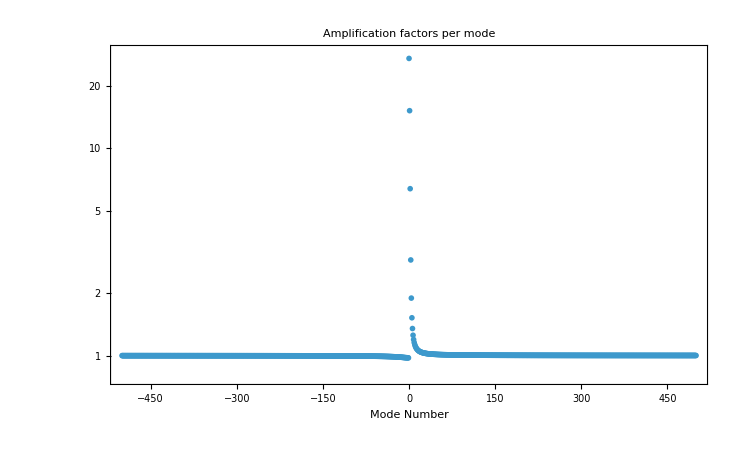

```mathematica
(* Plot amplification factors *)
ListLogPlot[Transpose[{Range[-size,size],ks}],PlotRange->{{0.8*Min[ks],kmax+2}},
Frame->{True,True,False,False},
FrameLabel->{Style["Mode Number", Black, Large],""}, LabelStyle->Directive[Larger,Black],
PlotLabel->Style["Amplification factors per mode", Black, Larger], PerformanceGoal->"Speed"]
```

```mathematica
(* Stroboscopic Plots for modes -3,-2,-1,0,1,2,3 *)
```

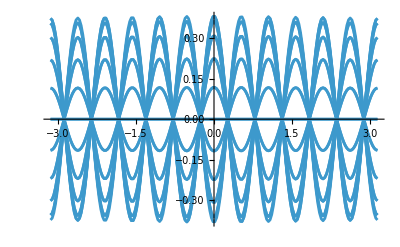
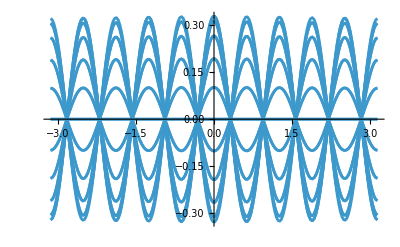
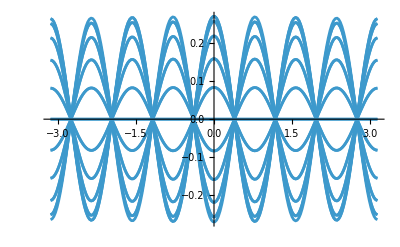
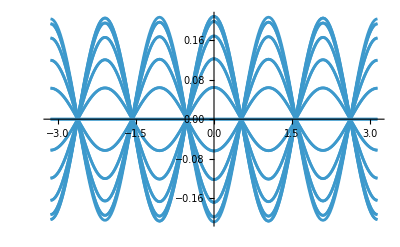
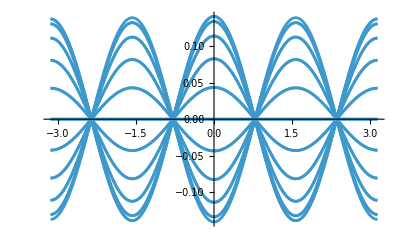
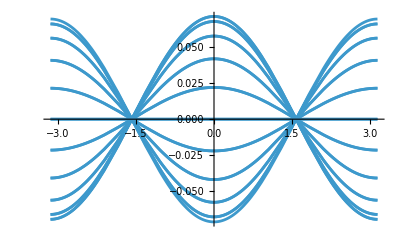
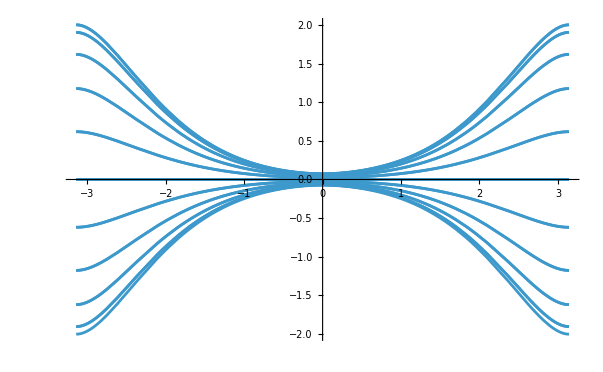
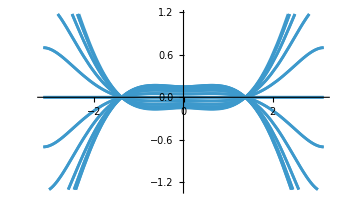

```mathematica
Table[Plot[Chop[xlcentroidstrobe[[size+i]]],{ψ,-Pi,Pi},PerformanceGoal->"Speed"],
{i,-5,5}
]
```

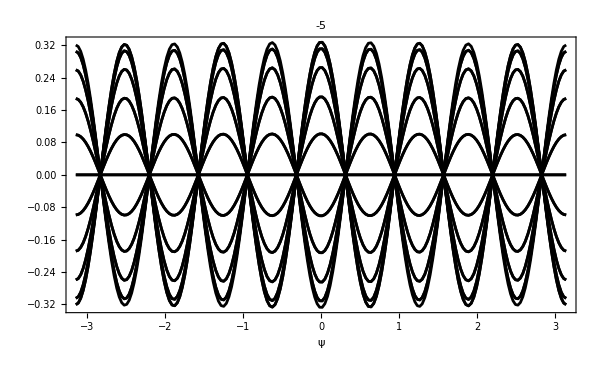
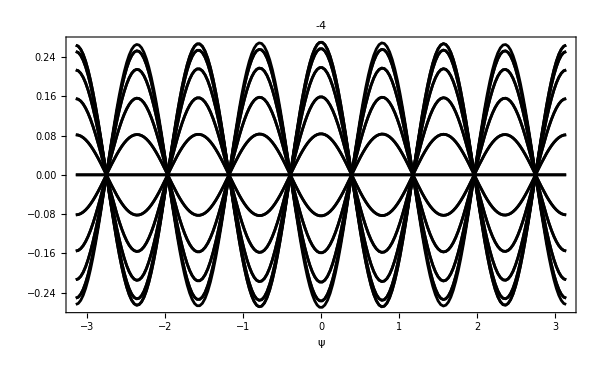
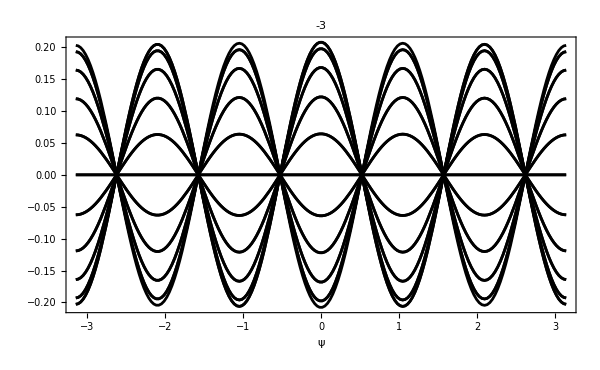
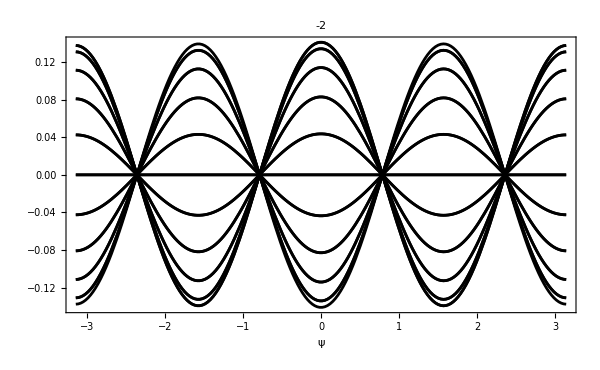
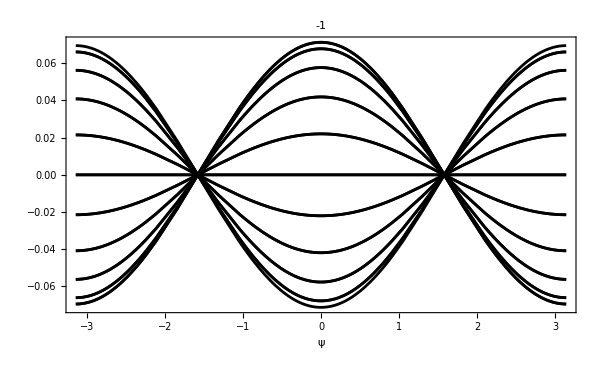
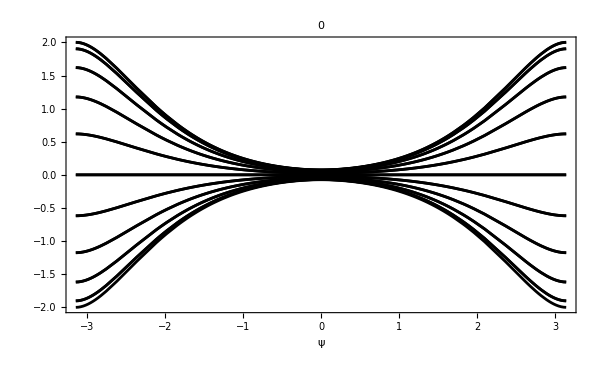
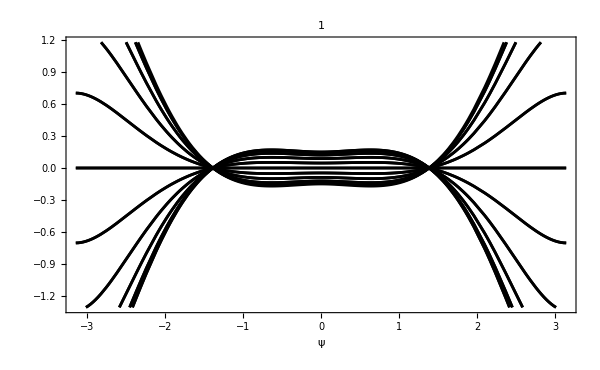
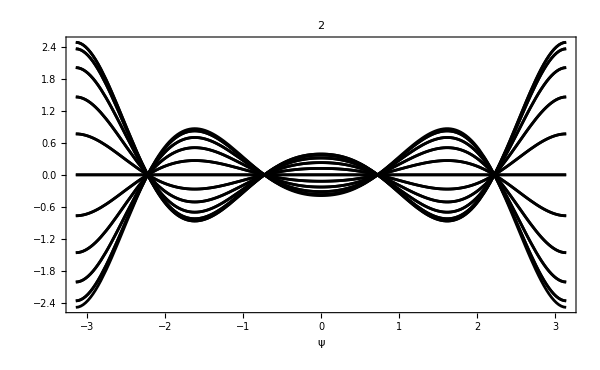

```mathematica
Table[Plot[Chop[xlcentroidstrobe[[size+i+1]]],{ψ,-Pi,Pi},PerformanceGoal->"Speed",
PlotStyle->{Black},
PlotLabel->Style[StringForm["`1`",i],Black],
FrameLabel->{ Style["ψ",45,Black],Style["",45,Black]},
FrameStyle->Black,Frame->True,ImageSize->600,
LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->30}],
{i,-5,5}
]
```